## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Test

```mathematica
kfinal={0.4709613222916442,-0.2550225519531524};
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

```mathematica
Tmuscan=Join[Table[{0.155,i},{i,0.,0.155,0.005}],Table[{0.155,i},{i,0.16,1.,0.05}]];
```

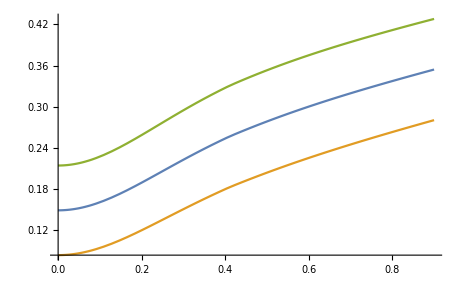

```mathematica
Plot[{mDcalmu[0.155,x,kfinal[[1]],kfinal[[2]]],mDcalmu[0.155,x,kfinall[[1]],kfinall[[2]]],mDcalmu[0.155,x,kfinalu[[1]],kfinalu[[2]]]},{x,0.,0.9}]
```

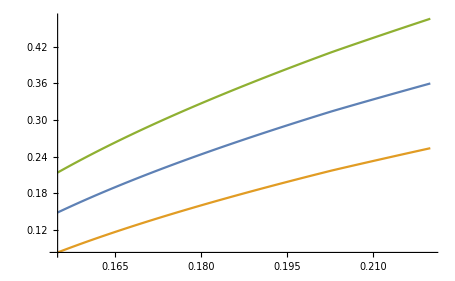

```mathematica
Plot[{mDcalmu[x,0,kfinal[[1]],kfinal[[2]]],mDcalmu[x,0,kfinall[[1]],kfinall[[2]]],mDcalmu[x,0,kfinalu[[1]],kfinalu[[2]]]},{x,0.155,0.22}]
```

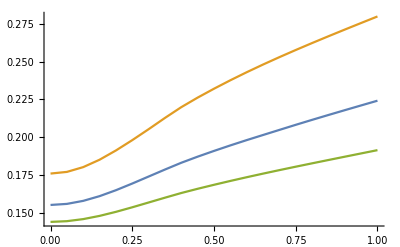

```mathematica
ListLinePlot[{Table[{μ,x/.FindRoot[mDcalmu[x,0,kfinal[[1]],kfinal[[2]]]==mDcalmu[0.155,μ,kfinal[[1]],kfinal[[2]]],{x,0.155}]},{μ,0.,1.,0.05}],Table[{μ,x/.FindRoot[mDcalmu[x,0,kfinall[[1]],kfinall[[2]]]==mDcalmu[0.155,μ,kfinal[[1]],kfinal[[2]]],{x,0.155}]},{μ,0.,1.,0.05}],Table[{μ,x/.FindRoot[mDcalmu[x,0,kfinalu[[1]],kfinalu[[2]]]==mDcalmu[0.155,μ,kfinal[[1]],kfinal[[2]]],{x,0.155}]},{μ,0.,1.,0.05}]}]
```